```mathematica
rawData10 =Transpose[
Import["/home/neofelia/Desktop/Bachelor/static lambda/histograms/n0l07range10width1.csv","Data", "HeaderLines"->1]];
value10 = rawData10[[3]];
counter10 = rawData10[[4]];
maxCounter = Max[counter10];
hist10 = Transpose[{value10, counter10/maxCounter}];

rawData20 =Transpose[
Import["/home/neofelia/Desktop/Bachelor/static lambda/histograms/n0l07range20width1.csv","Data", "HeaderLines"->1]];
value20 = rawData20[[3]];
counter20 = rawData20[[4]];
maxCounter20 = Max[counter20];
hist20 = Transpose[{value20, counter20/maxCounter20}];

rawData30 =Transpose[
Import["/home/neofelia/Desktop/Bachelor/static lambda/histograms/n0l07range30width1.csv","Data", "HeaderLines"->1]];
value30 = rawData30[[3]];
counter30 = rawData30[[4]];
maxCounter30 = Max[counter30];
hist30 = Transpose[{value30, counter30/maxCounter30}];

rawData40 =Transpose[
Import["/home/neofelia/Desktop/Bachelor/static lambda/histograms/n0l07range40width1.csv","Data", "HeaderLines"->1]];
value40 = rawData40[[3]];
counter40 = rawData40[[4]];
maxCounter40 = Max[counter40];
hist40 = Transpose[{value40, counter40/maxCounter40}];
```

```mathematica
rawData110 =Transpose[
Import["/home/neofelia/Desktop/Bachelor/static lambda/histograms/n0l07range110width1.csv","Data", "HeaderLines"->1]];
value110 = rawData110[[3]];
counter110 = rawData110[[4]];
maxCounter110 = Max[counter110];
hist110 = Transpose[{value110, counter110/maxCounter110}];

rawData120 =Transpose[
Import["/home/neofelia/Desktop/Bachelor/static lambda/histograms/n0l07range120width1.csv","Data", "HeaderLines"->1]];
value120 = rawData120[[3]];
counter120 = rawData120[[4]];
maxCounter120 = Max[counter120];
hist120 = Transpose[{value120, counter120/maxCounter120}];

rawData130 =Transpose[
Import["/home/neofelia/Desktop/Bachelor/static lambda/histograms/n0l07range130width1.csv","Data", "HeaderLines"->1]];
value130 = rawData130[[3]];
counter130 = rawData130[[4]];
maxCounter130 = Max[counter130];
hist130 = Transpose[{value130, counter130/maxCounter130}];

rawData140 =Transpose[
Import["/home/neofelia/Desktop/Bachelor/static lambda/histograms/n0l07range140width1.csv","Data", "HeaderLines"->1]];
value140 = rawData140[[3]];
counter140 = rawData140[[4]];
maxCounter140 = Max[counter140];
hist140 = Transpose[{value140, counter140/maxCounter140}];
```

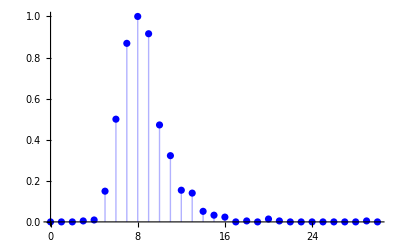

```mathematica
ListPlot[{hist10},Filling->Axis, PlotRange->All, PlotStyle->Blue]
```

{A0→7.77589,σ→3.0537,μ→8.11641}

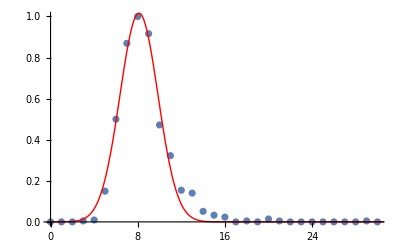

```mathematica
nlm10 = NonlinearModelFit[hist10,A0/Sqrt[2*π*σ^2]*ⅇ^(- (x-μ)^2/(2*σ) ),{{A0},{σ},{μ, 10}},x];
Normal[nlm10];
 nlm10["BestFitParameters"]
(*nlm["FitResiduals"] ;  *)
Show[ ListPlot[hist10,  PlotRange->All],Plot[nlm10[x],{x,0,200} , PlotRange->{{0,200},{0,100}}, PlotStyle->{Thick, Red} ]]
```

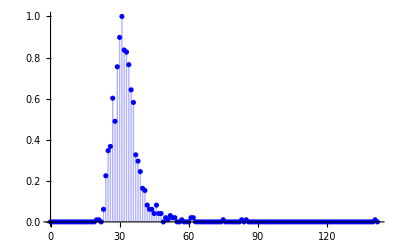

```mathematica
ListPlot[{hist20},Filling->Axis, PlotRange->All, PlotStyle->Blue]
```

{A0→7.77589,σ→3.0537,μ→8.11641}

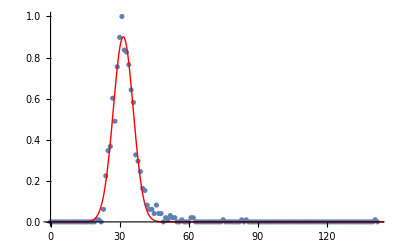

```mathematica
nlm20 = NonlinearModelFit[hist20,A0/Sqrt[2*π*σ^2]*ⅇ^(- (x-μ)^2/(2*σ) ),{{A0},{σ},{μ, 40}},x];
Normal[nlm20];
 nlm10["BestFitParameters"]
(*nlm["FitResiduals"] ;  *)
Show[ ListPlot[hist20,  PlotRange->All],Plot[nlm20[x],{x,0,200} , PlotRange->{{0,200},{0,100}}, PlotStyle->{Thick, Red} ]]
```

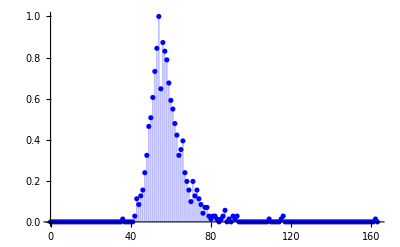

```mathematica
ListPlot[{hist30},Filling->Axis, PlotRange->All, PlotStyle->Blue]
```

{A0→85.0576,σ→41.2483,μ→56.1274}

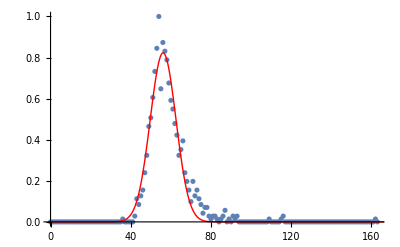

```mathematica
nlm30 = NonlinearModelFit[hist30,A0/Sqrt[2*π*σ^2]*ⅇ^(- (x-μ)^2/(2*σ) ),{{A0},{σ},{μ, 70}},x];
Normal[nlm30];
 nlm30["BestFitParameters"]
(*nlm["FitResiduals"] ;  *)
Show[ ListPlot[hist30,  PlotRange->All],Plot[nlm30[x],{x,0,200} , PlotRange->{{0,200},{0,100}}, PlotStyle->{Thick, Red} ]]
```

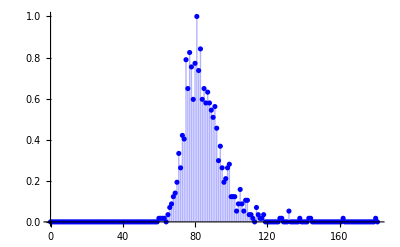

```mathematica
ListPlot[{hist40},Filling->Axis, PlotRange->All, PlotStyle->Blue]
```

{A0→145.53,σ→74.7055,μ→82.4672}

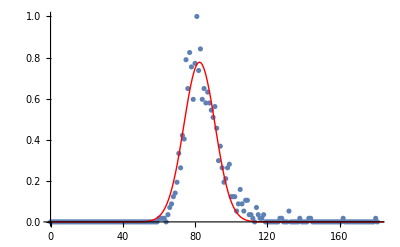

```mathematica
nlm40 = NonlinearModelFit[hist40,A0/Sqrt[2*π*σ^2]*ⅇ^(- (x-μ)^2/(2*σ) ),{{A0},{σ},{μ, 120}},x];
Normal[nlm40];
 nlm40["BestFitParameters"]
(*nlm["FitResiduals"] ;  *)
Show[ ListPlot[hist40,  PlotRange->All],Plot[nlm40[x],{x,0,200} , PlotRange->{{0,200},{0,100}}, PlotStyle->{Thick, Red} ]]
```

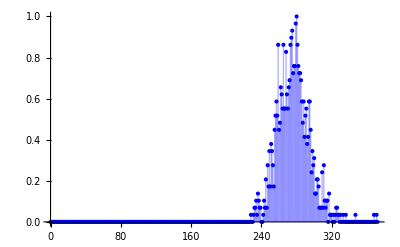

```mathematica
ListPlot[{hist110},Filling->Axis, PlotRange->All, PlotStyle->Blue]
```

{A0→577.116,σ→287.114,μ→275.207}

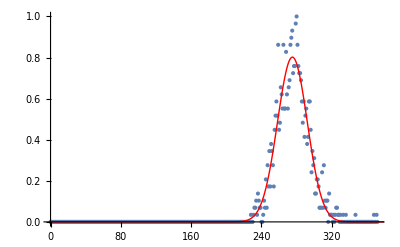

```mathematica
nlm110 = NonlinearModelFit[hist110,A0/Sqrt[2*π*σ^2]*ⅇ^(- (x-μ)^2/(2*σ) ),{{A0},{σ},{μ, 250}},x];
Normal[nlm110];
 nlm110["BestFitParameters"]
(*nlm["FitResiduals"] ;  *)
Show[ ListPlot[hist110,  PlotRange->All],Plot[nlm110[x],{x,0,600} , PlotRange->{{0,600},{0,100}}, PlotStyle->{Thick, Red} ]]
```

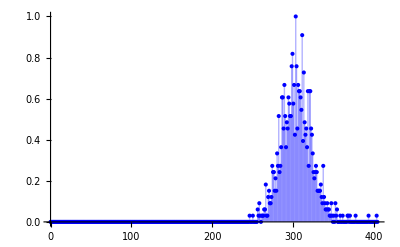

```mathematica
ListPlot[{hist120},Filling->Axis, PlotRange->All, PlotStyle->Blue]
```

{A0→542.631,σ→325.662,μ→303.349}

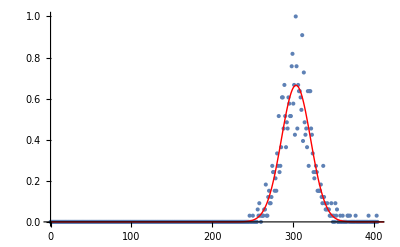

```mathematica
nlm120 = NonlinearModelFit[hist120,A0/Sqrt[2*π*σ^2]*ⅇ^(- (x-μ)^2/(2*σ) ),{{A0},{σ},{μ, 350}},x];
Normal[nlm120];
 nlm120["BestFitParameters"]
(*nlm["FitResiduals"] ;  *)
Show[ ListPlot[hist120,  PlotRange->All],Plot[nlm120[x],{x,0,600} , PlotRange->{{0,600},{0,100}}, PlotStyle->{Thick, Red} ]]
```

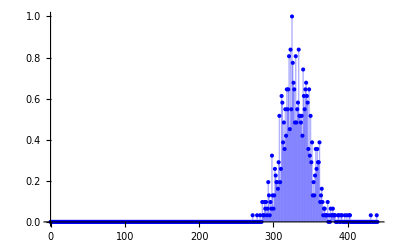

```mathematica
ListPlot[{hist130},Filling->Axis, PlotRange->All, PlotStyle->Blue]
```

{A0→607.982,σ→358.128,μ→330.471}

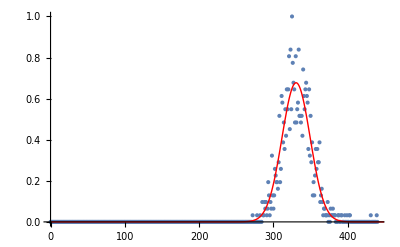

```mathematica
nlm130 = NonlinearModelFit[hist130,A0/Sqrt[2*π*σ^2]*ⅇ^(- (x-μ)^2/(2*σ) ),{{A0},{σ},{μ, 400}},x];
Normal[nlm130];
 nlm130["BestFitParameters"]
(*nlm["FitResiduals"] ;  *)
Show[ ListPlot[hist130,  PlotRange->All],Plot[nlm130[x],{x,0,600} , PlotRange->{{0,600},{0,100}}, PlotStyle->{Thick, Red} ]]
```

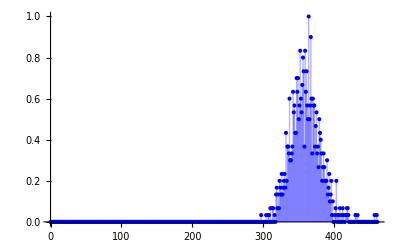

```mathematica
ListPlot[{hist140},Filling->Axis, PlotRange->All, PlotStyle->Blue]
```

{A0→650.081,σ→386.417,μ→358.249}

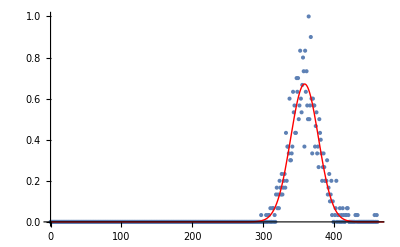

```mathematica
nlm140 = NonlinearModelFit[hist140,A0/Sqrt[2*π*σ^2]*ⅇ^(- (x-μ)^2/(2*σ) ),{{A0},{σ},{μ, 350}},x];
Normal[nlm140];
 nlm140["BestFitParameters"]
(*nlm["FitResiduals"] ;  *)
Show[ ListPlot[hist140,  PlotRange->All],Plot[nlm140[x],{x,0,800} , PlotRange->{{0,800},{0,100}}, PlotStyle->{Thick, Red} ]]
```